### Speed test of simple LQR gains for random 8x8 linear system

Time = 0.00231553

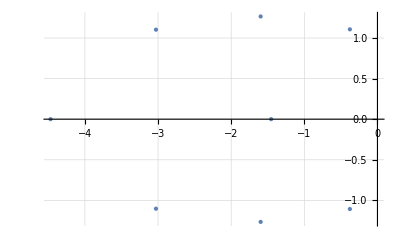

```mathematica
Clear["Global`*"];
a=RandomVariate[NormalDistribution[],{8,8}];
b=RandomVariate[NormalDistribution[],{8,1}];
ssm=StateSpaceModel[{a,b}];
{q,r}=IdentityMatrix/@{8,1};
MatrixForm/@{q,r};
{time1,K} = RepeatedTiming[LQRegulatorGains[ssm,{q,r}]];
K = K[[1]];
poles = Eigenvalues[a - KroneckerProduct[b,K]];
Print["Time = ",time1];
ListPlot[ReIm /@ poles,PlotStyle->PointSize[Large],GridLines->Automatic]
```

### Design LQR feedback by Linearizing the system

```mathematica
ClearAll["Global`*"];
Remove["Global`*"];
(*ICs - Initial Conditions *) (* Error while cosntraining u *)


CalculateSMatrix[x1a_,xdot1a_,θ1a_,θdot1a_,u1a_,τ_,A_]:=Module[{x,L,RHS,xdot,θ,θdot,u,K,S,soltn,Af,Bf,Q,fx,xState,R,Mf,x2dot,θ2dot,S0,sol2,t},xState={x,xdot,θ,θdot};x2dot=(u+A θdot^2 Sin[θ]+A Cos[θ] Sin[θ])/(1-A Cos[θ]^2);θ2dot=(-Sin[θ]-Cos[θ] (u+A θdot^2 Sin[θ]))/(1-A Cos[θ]^2);fx={xdot,x2dot,θdot,θ2dot};L=u^2/2;Af=fxxState;Bf=D[fx, u];Q=LxStatexState;Mf=D[L, u]xState;R=D[L, {u,2}];S0={{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}};RHS[t_]:=IdentityMatrix[4]+Transpose[Af].S[t]+S[t].Af-KroneckerProduct[S[t].Bf,Transpose[Bf].S[t]]/.{x->x1a[τ-t],xdot->xdot1a[τ-t],θ->θ1a[τ-t],θdot->θdot1a[τ-t],u->u1a[τ-t]};sol2=S/.NDSolve[{S'[t]==RHS[t],S[0]==S0},S,{t,0,τ}];S=sol2⟦1⟧]
CalculateGains[x1a_,xdot1a_,θ1a_,θdot1a_,u1a_,time_,A_,τ_,S_]:= Module[{x,L,RHS,xdot,θ,θdot,u,K,Af,Bf,Q,fx,xState,R,Mf,x2dot,θ2dot,S0,sol2,t},
xState = {x,xdot,θ,θdot};
x2dot = 1/(1-A Cos[θ]^2) (u+A θdot^2 Sin[θ]+A Cos[θ] Sin[θ]);
θ2dot= 1/(1-A Cos[θ]^2) (-Sin[θ]-Cos[θ] (u+A θdot^2 Sin[θ]));
fx = {xdot,x2dot,θdot,θ2dot};
Bf = D[fx,u] ;(*For 1D stuff use D*)
K = (Bfᵀ.S[τ - time])/. {x-> x1a[time], xdot -> xdot1a[time], θ ->θ1a[time], θdot -> θdot1a[time], u -> u1a[time]};
K
]

ffCartPendulum[ICs_,systemData_]:=
Module[{n,τ,τ1,A,time1,time2,order,maxIter,maxError,uMax,maxCount,initGuess,maxJ,frootNew,errorNew,InitGuess,J,S,K,count,error,x,dist,xdot,f,θ,θdot,λ1,λ2,λ3,λ4,Δt,bcs,eqns,sv,froot,xff,xdotff,xff0,xdotff0,θff0,θdotff0,uff0,θff,θdotff,uff,λ1ff0,λ2ff0,λ3ff0,λ4ff0,i,xGuess = Table[Subscript[xGuess, i],{i,0,n}]},Δt=τ/n;
{n,τ,τ1,A,order,maxIter,maxError,uMax,maxCount,initGuess,maxJ} = systemData;
f[{x_,xdot_,θ_,θdot_,λ1_,λ2_,λ3_,λ4_}]:={
	xdot,
	1/(1-A Cos[θ]^2) (A θdot^2 Sin[θ]+1/(1-A Cos[θ]^2) (λ4 Cos[θ]-λ2)+A Cos[θ] Sin[θ]),
	θdot,
	1/(1-A Cos[θ]^2) (-(1/(1-A Cos[θ]^2))(-λ2 Cos[θ]+λ4 Cos[θ]^2)-Sin[θ]-A θdot^2 Cos[θ] Sin[θ]),
	0,
	-λ1,
	1/((-1+A Cos[θ]^2)^3)(A^2 (A θdot^2 λ2-λ4) Cos[θ]^5+A^3 (λ2-θdot^2 λ4) Cos[θ]^6-1/2 A^2 (λ2-θdot^2 λ4) Cos[θ]^4 (4-A+A Cos[2 θ])-A Cos[θ]^2 (-λ2+θdot^2 λ4+3 λ2 λ4 Sin[θ])+Cos[θ] (A θdot^2 λ2-λ4+(2 A λ2^2+λ4^2) Sin[θ]-2 A^2 θdot^2 λ2 Sin[θ]^2)+A Cos[θ]^3 (-2 A θdot^2 λ2+2 λ4+λ4^2 Sin[θ]+2 A (A θdot^2 λ2-λ4) Sin[θ]^2)+Sin[θ] (-λ2 λ4-A (λ2-θdot^2 λ4) Sin[θ]+A λ4 Sin[2 θ])),
	4 /(A Cos[2 θ]+A-2) (A θdot Sin[θ] (λ2-λ4 Cos[θ]))-λ3
};

InitGuess = initGuess;
xGuess = Table[If[i != -1,Subscript[xGuess, i+1] = Subscript[xGuess, i] +Δt*f[Subscript[xGuess, i]],Subscript[xGuess, 0] = {ICs[[1]],ICs[[2]],ICs[[3]],ICs[[4]],InitGuess[[1]],InitGuess[[2]],InitGuess[[3]],InitGuess[[4]]}],{i,-1,n-1}];

bcs={Subscript[x, 0]==ICs[[1]],Subscript[xdot, 0]==ICs[[2]],Subscript[x, n]==Subscript[xdot, n]==0,Subscript[θ, 0]==ICs[[3]],Subscript[θdot, 0]==ICs[[4]],Subscript[θdot, n]==0,Subscript[θ, n]==π};
eqns=Flatten[Join[bcs,Table[Thread[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}==
1/2 Δt (f[{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]}]+
f[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}])+
{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]}],{i,1,n}]]];

sv = Flatten[Table[{{Subscript[x, i],xGuess[[i+1]][[1]]},{Subscript[xdot, i],xGuess[[i+1]][[2]]},{Subscript[θ, i],xGuess[[i+1]][[3]]},{Subscript[θdot, i],xGuess[[i+1]][[4]]},
					{Subscript[λ1, i],xGuess[[i+1]][[5]]},{Subscript[λ2, i],xGuess[[i+1]][[6]]},{Subscript[λ3, i],xGuess[[i+1]][[7]]},{Subscript[λ4, i],xGuess[[i+1]][[8]]}},{i,0,n}],1];

froot=FindRoot[eqns,sv,MaxIterations->maxIter];
error = Norm[Flatten[Join[{Subscript[x, n],Subscript[xdot, n],Subscript[θ, n],Subscript[θdot, n]} - {0,0,π,0},{Subscript[x, 0],Subscript[xdot, 0],Subscript[θ, 0],Subscript[θdot, 0]} - ICs,Table[Thread[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}-(1/2 Δt (f[{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]}]+f[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}])+{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]})],{i,1,n}]]]/.froot,"Frobenius"];

count = 0;

Print["Error First Guess = ",error];

uff0=ListInterpolation[Table[1/(1-A Cos[Subscript[θ, i]]^2) (Subscript[λ4, i]Cos[Subscript[θ, i]]-Subscript[λ2, i]),{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
J = NIntegrate[uff0[t]^2,{t,0,τ}];
While[((error > maxError) || (J > maxJ)) && count <= maxCount ,
InitGuess = {RandomReal[{-1,1}],RandomReal[{-1,1}],RandomReal[{-1,1}],RandomReal[{-1,1}]};
xGuess = Table[If[i != -1,Subscript[xGuess, i+1] = Subscript[xGuess, i] +Δt*f[Subscript[xGuess, i]],Subscript[xGuess, 0] = {ICs[[1]],ICs[[2]],ICs[[3]],ICs[[4]],InitGuess[[1]],InitGuess[[2]],InitGuess[[3]],InitGuess[[4]]}],{i,-1,n-1}];
sv = Flatten[Table[{{Subscript[x, i],xGuess[[i+1]][[1]]},{Subscript[xdot, i],xGuess[[i+1]][[2]]},{Subscript[θ, i],xGuess[[i+1]][[3]]},{Subscript[θdot, i],xGuess[[i+1]][[4]]},
					{Subscript[λ1, i],xGuess[[i+1]][[5]]},{Subscript[λ2, i],xGuess[[i+1]][[6]]},{Subscript[λ3, i],xGuess[[i+1]][[7]]},{Subscript[λ4, i],xGuess[[i+1]][[8]]}},{i,0,n}],1];

frootNew=FindRoot[eqns,sv,MaxIterations->maxIter];
errorNew = Norm[Flatten[Join[{Subscript[x, n],Subscript[xdot, n],Subscript[θ, n],Subscript[θdot, n]} - {0,0,π,0},{Subscript[x, 0],Subscript[xdot, 0],Subscript[θ, 0],Subscript[θdot, 0]} - ICs,Table[Thread[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}-(1/2 Δt (f[{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]}]+f[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}])+{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]})],{i,1,n}]]]/.frootNew,"Frobenius"];
If[errorNew <= error,froot = frootNew;error = errorNew;
uff0=ListInterpolation[Table[1/(1-A Cos[Subscript[θ, i]]^2) (Subscript[λ4, i]Cos[Subscript[θ, i]]-Subscript[λ2, i]),{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
J = NIntegrate[uff0[t]^2,{t,0,τ}];
,_];
count = count+1;

Print["Count Shooting= ",count,"    Error New = ",errorNew,"    Error Min = ",error];

];


xff0=ListInterpolation[Table[Subscript[x, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
xdotff0=ListInterpolation[Table[Subscript[xdot, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
θff0=ListInterpolation[Table[Subscript[θ, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
θdotff0=ListInterpolation[Table[Subscript[θdot, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
λ1ff0 = ListInterpolation[Table[Subscript[λ1, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
λ2ff0 = ListInterpolation[Table[Subscript[λ2, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
λ3ff0 = ListInterpolation[Table[Subscript[λ3, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
λ4ff0 = ListInterpolation[Table[Subscript[λ3, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];

uff0=ListInterpolation[Table[1/(1-A Cos[Subscript[θ, i]]^2) (Subscript[λ4, i]Cos[Subscript[θ, i]]-Subscript[λ2, i]),{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];

xff[t_]:=Piecewise[{{xff0[t],0<=t<=τ}},0];
xdotff[t_]:=Piecewise[{{xdotff0[t],0<=t<=τ}},0];
θff[t_]:=Piecewise[{{θff0[t],0<=t<=τ}},π];
θdotff[t_]:=Piecewise[{{θdotff0[t],0<=t<=τ}},0];
uff[t_]:=Piecewise[{{uff0[t],0<=t<=τ}},0];
J = NIntegrate[uff0[t]^2,{t,0,τ}];
S = CalculateSMatrix[xff,xdotff,θff,θdotff,uff,τ,A];
K[time_] := CalculateGains[xff,xdotff,θff,θdotff,uff,time,A,τ,S];
{xff,xdotff,θff,θdotff,uff,λ1ff0,λ2ff0,λ3ff0,λ4ff0,J,K}]

ffCartPendulumTimed[ICs_,systemData_]:=
Module[{n,τ,τ1,A,time1,time2,order,maxIter,maxError,uMax,maxCount,initGuess,maxJ,frootNew,errorNew,InitGuess,J,S,K,count,error,x,dist,xdot,f,θ,θdot,λ1,λ2,λ3,λ4,Δt,bcs,eqns,sv,froot,xff,xdotff,xff0,xdotff0,θff0,θdotff0,uff0,θff,θdotff,uff,λ1ff0,λ2ff0,λ3ff0,λ4ff0,i,xGuess = Table[Subscript[xGuess, i],{i,0,n}]},Δt=τ/n;
{n,τ,τ1,A,order,maxIter,maxError,uMax,maxCount,initGuess,maxJ} = systemData;
f[{x_,xdot_,θ_,θdot_,λ1_,λ2_,λ3_,λ4_}]:={
	xdot,
	1/(1-A Cos[θ]^2) (A θdot^2 Sin[θ]+1/(1-A Cos[θ]^2) (λ4 Cos[θ]-λ2)+A Cos[θ] Sin[θ]),
	θdot,
	1/(1-A Cos[θ]^2) (-(1/(1-A Cos[θ]^2))(-λ2 Cos[θ]+λ4 Cos[θ]^2)-Sin[θ]-A θdot^2 Cos[θ] Sin[θ]),
	0,
	-λ1,
	1/((-1+A Cos[θ]^2)^3)(A^2 (A θdot^2 λ2-λ4) Cos[θ]^5+A^3 (λ2-θdot^2 λ4) Cos[θ]^6-1/2 A^2 (λ2-θdot^2 λ4) Cos[θ]^4 (4-A+A Cos[2 θ])-A Cos[θ]^2 (-λ2+θdot^2 λ4+3 λ2 λ4 Sin[θ])+Cos[θ] (A θdot^2 λ2-λ4+(2 A λ2^2+λ4^2) Sin[θ]-2 A^2 θdot^2 λ2 Sin[θ]^2)+A Cos[θ]^3 (-2 A θdot^2 λ2+2 λ4+λ4^2 Sin[θ]+2 A (A θdot^2 λ2-λ4) Sin[θ]^2)+Sin[θ] (-λ2 λ4-A (λ2-θdot^2 λ4) Sin[θ]+A λ4 Sin[2 θ])),
	4 /(A Cos[2 θ]+A-2) (A θdot Sin[θ] (λ2-λ4 Cos[θ]))-λ3
};

InitGuess = initGuess;
xGuess = Table[If[i != -1,Subscript[xGuess, i+1] = Subscript[xGuess, i] +Δt*f[Subscript[xGuess, i]],Subscript[xGuess, 0] = {ICs[[1]],ICs[[2]],ICs[[3]],ICs[[4]],InitGuess[[1]],InitGuess[[2]],InitGuess[[3]],InitGuess[[4]]}],{i,-1,n-1}];

bcs={Subscript[x, 0]==ICs[[1]],Subscript[xdot, 0]==ICs[[2]],Subscript[x, n]==Subscript[xdot, n]==0,Subscript[θ, 0]==ICs[[3]],Subscript[θdot, 0]==ICs[[4]],Subscript[θdot, n]==0,Subscript[θ, n]==π};
eqns=Flatten[Join[bcs,Table[Thread[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}==
1/2 Δt (f[{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]}]+
f[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}])+
{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]}],{i,1,n}]]];

sv = Flatten[Table[{{Subscript[x, i],xGuess[[i+1]][[1]]},{Subscript[xdot, i],xGuess[[i+1]][[2]]},{Subscript[θ, i],xGuess[[i+1]][[3]]},{Subscript[θdot, i],xGuess[[i+1]][[4]]},
					{Subscript[λ1, i],xGuess[[i+1]][[5]]},{Subscript[λ2, i],xGuess[[i+1]][[6]]},{Subscript[λ3, i],xGuess[[i+1]][[7]]},{Subscript[λ4, i],xGuess[[i+1]][[8]]}},{i,0,n}],1];

{time1,froot}=Timing[FindRoot[eqns,sv,MaxIterations->maxIter]];
error = Norm[Flatten[Join[{Subscript[x, n],Subscript[xdot, n],Subscript[θ, n],Subscript[θdot, n]} - {0,0,π,0},{Subscript[x, 0],Subscript[xdot, 0],Subscript[θ, 0],Subscript[θdot, 0]} - ICs,Table[Thread[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}-(1/2 Δt (f[{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]}]+f[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}])+{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]})],{i,1,n}]]]/.froot,"Frobenius"];

count = 0;

Print["Error First Guess = ",error];

uff0=ListInterpolation[Table[1/(1-A Cos[Subscript[θ, i]]^2) (Subscript[λ4, i]Cos[Subscript[θ, i]]-Subscript[λ2, i]),{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
J = NIntegrate[uff0[t]^2,{t,0,τ}];
While[((error > maxError) || (J > maxJ)) && count <= maxCount ,
InitGuess = {RandomReal[{-1,1}],RandomReal[{-1,1}],RandomReal[{-1,1}],RandomReal[{-1,1}]};
xGuess = Table[If[i != -1,Subscript[xGuess, i+1] = Subscript[xGuess, i] +Δt*f[Subscript[xGuess, i]],Subscript[xGuess, 0] = {ICs[[1]],ICs[[2]],ICs[[3]],ICs[[4]],InitGuess[[1]],InitGuess[[2]],InitGuess[[3]],InitGuess[[4]]}],{i,-1,n-1}];
sv = Flatten[Table[{{Subscript[x, i],xGuess[[i+1]][[1]]},{Subscript[xdot, i],xGuess[[i+1]][[2]]},{Subscript[θ, i],xGuess[[i+1]][[3]]},{Subscript[θdot, i],xGuess[[i+1]][[4]]},
					{Subscript[λ1, i],xGuess[[i+1]][[5]]},{Subscript[λ2, i],xGuess[[i+1]][[6]]},{Subscript[λ3, i],xGuess[[i+1]][[7]]},{Subscript[λ4, i],xGuess[[i+1]][[8]]}},{i,0,n}],1];

frootNew=FindRoot[eqns,sv,MaxIterations->maxIter];
errorNew = Norm[Flatten[Join[{Subscript[x, n],Subscript[xdot, n],Subscript[θ, n],Subscript[θdot, n]} - {0,0,π,0},{Subscript[x, 0],Subscript[xdot, 0],Subscript[θ, 0],Subscript[θdot, 0]} - ICs,Table[Thread[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}-(1/2 Δt (f[{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]}]+f[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}])+{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]})],{i,1,n}]]]/.frootNew,"Frobenius"];
If[errorNew <= error,froot = frootNew;error = errorNew;
uff0=ListInterpolation[Table[1/(1-A Cos[Subscript[θ, i]]^2) (Subscript[λ4, i]Cos[Subscript[θ, i]]-Subscript[λ2, i]),{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
J = NIntegrate[uff0[t]^2,{t,0,τ}];
,_];
count = count+1;

Print["Count Shooting= ",count,"    Error New = ",errorNew,"    Error Min = ",error];

];


xff0=ListInterpolation[Table[Subscript[x, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
xdotff0=ListInterpolation[Table[Subscript[xdot, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
θff0=ListInterpolation[Table[Subscript[θ, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
θdotff0=ListInterpolation[Table[Subscript[θdot, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
λ1ff0 = ListInterpolation[Table[Subscript[λ1, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
λ2ff0 = ListInterpolation[Table[Subscript[λ2, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
λ3ff0 = ListInterpolation[Table[Subscript[λ3, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
λ4ff0 = ListInterpolation[Table[Subscript[λ3, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];

uff0=ListInterpolation[Table[1/(1-A Cos[Subscript[θ, i]]^2) (Subscript[λ4, i]Cos[Subscript[θ, i]]-Subscript[λ2, i]),{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];

xff[t_]:=Piecewise[{{xff0[t],0<=t<=τ}},0];
xdotff[t_]:=Piecewise[{{xdotff0[t],0<=t<=τ}},0];
θff[t_]:=Piecewise[{{θff0[t],0<=t<=τ}},π];
θdotff[t_]:=Piecewise[{{θdotff0[t],0<=t<=τ}},0];
uff[t_]:=Piecewise[{{uff0[t],0<=t<=τ}},0];
J = NIntegrate[uff0[t]^2,{t,0,τ}];
{time2,S} = Timing[CalculateSMatrix[xff,xdotff,θff,θdotff,uff,τ,A]];
K[time_] := CalculateGains[xff,xdotff,θff,θdotff,uff,time,A,τ,S];
{xff,xdotff,θff,θdotff,uff,λ1ff0,λ2ff0,λ3ff0,λ4ff0,J,K,time1,time2}]


testSwingUp[ICs_,τ_,τ1_,uff0_,A_]:=Module[{eq,init,x,xdot,θ,θdot,xs,xdots,θs,θdots,t,J},
eq={x'[t]==xdot[t],xdot'[t]==1/(1-A Cos[θ[t]]^2) (uff0[t]+A θdot[t]^2 Sin[θ[t]]+A Cos[θ[t]] Sin[θ[t]]),θ'[t]==θdot[t],θdot'[t]==1/(1-A Cos[θ[t]]^2) (-Sin[θ[t]]-Cos[θ[t]] (uff0[t]+A θdot[t]^2 Sin[θ[t]]))};
init={x[0]==ICs[[1]],xdot[0]==ICs[[2]],θ[0]==ICs[[3]],θdot[0]==ICs[[4]]};
{xs,xdots,θs,θdots}=NDSolveValue[{eq,init},{x,xdot,θ,θdot},{t,0,τ1},Method->{"DiscontinuityProcessing"->None}];
J = NIntegrate[uff0[t]^2,{t,0,τ}];
{xs,xdots,θs,θdots,uff0,J}]



testWithFB[ICs_,τ_,τ1_,xff0_,xdotff0_,θff0_,θdotff0_,uff0_,A_,K_]:=Module[{eq,init,θ,θdot,θff,θdotff,x,xdot,xff,xdotff,uff,t,κ1,κ2,κ3,κ4,ufb,u,θs,θdots,xs,xdots,us,J},
κ1=κ2=3;  (* lqr for q=r for balancing pendulum *)
κ3 = -0.1;κ4 = -0.65;
xff[t_]:=Piecewise[{{xff0[t],0<=t<=τ}},0];
xdotff[t_]:=Piecewise[{{xdotff0[t],0<=t<=τ}},0];
θff[t_]:=Piecewise[{{θff0[t],0<=t<=τ}},π];
θdotff[t_]:=Piecewise[{{θdotff0[t],0<=t<=τ}},0];
uff[t_]:=Piecewise[{{uff0[t],0<=t<=τ}},0];
ufb[t_] := Piecewise[{{K[t].{xff[t]-x[t],xdotff[t]-xdot[t],θff[t]-θ[t],θdotff[t]-θdot[t]},0<=t<=τ}},κ1(θff[t]-θ[t])+κ2 (θdotff[t]-θdot[t])+κ3(xff[t]-x[t])+κ4 (xdotff[t]-xdot[t])];
u[t_]:=uff[t]+ufb[t];

eq={x'[t]==xdot[t],xdot'[t]==1/(1-A Cos[θ[t]]^2) (u[t]+A θdot[t]^2 Sin[θ[t]]+A Cos[θ[t]] Sin[θ[t]]),θ'[t]==θdot[t],θdot'[t]==1/(1-A Cos[θ[t]]^2) (-Sin[θ[t]]-Cos[θ[t]] (u[t]+A θdot[t]^2 Sin[θ[t]]))};

init={x[0]==ICs[[1]],xdot[0]==ICs[[2]],θ[0]==ICs[[3]],θdot[0]==ICs[[4]]};

{xs,xdots,θs,θdots}=NDSolveValue[{eq,init},{x,xdot,θ,θdot},{t,0,τ1},Method->{"DiscontinuityProcessing"->None}];
us[t_]:=uff[t]+Piecewise[{{K[t].{xff[t]-xs[t],xdotff[t]-xdots[t],θff[t]-θs[t],θdotff[t]-θdots[t]},0<=t<=τ}},κ1(θff[t]-θs[t])+κ2 (θdotff[t]-θdots[t])+κ3(xff[t]-xs[t])+κ4 (xdotff[t]-xdots[t])];
J = NIntegrate[us[t]^2,{t,0,τ}];
{xs,xdots,θs,θdots,us,J}]

testWithFBClipped[ICs_,τ_,τ1_,xff0_,xdotff0_,θff0_,θdotff0_,uff0_,A_,uBound_,K_]:=Module[{eq,init,θ,θdot,θff,θdotff,x,xdot,xff,xdotff,uff,t,κ1,κ2,κ3,κ4,ufb,u,θs,θdots,xs,xdots,us,J},
{κ1,κ2,κ3,κ4} = {-0.999999999999936,-3.7234851629978962,7.432170879533125,7.229404929229439};

κ1=κ2=3;  (* lqr for q=r for balancing pendulum *)

κ3 = -0.1;κ4 = -0.65;
xff[t_]:=Piecewise[{{xff0[t],0<=t<=τ}},0];
xdotff[t_]:=Piecewise[{{xdotff0[t],0<=t<=τ}},0];
θff[t_]:=Piecewise[{{θff0[t],0<=t<=τ}},π];
θdotff[t_]:=Piecewise[{{θdotff0[t],0<=t<=τ}},0];
uff[t_]:=Piecewise[{{uff0[t],0<=t<=τ}},0];
ufb[t_] := Piecewise[{{K[t].{xff[t]-x[t],xdotff[t]-xdot[t],θff[t]-θ[t],θdotff[t]-θdot[t]},0<=t<=τ}},κ1(θff[t]-θ[t])+κ2 (θdotff[t]-θdot[t])+κ3(xff[t]-x[t])+κ4 (xdotff[t]-xdot[t])];
u[t_]:= Clip[uff[t]+ufb[t],{-uBound,uBound}];

eq={x'[t]==xdot[t],xdot'[t]==1/(1-A Cos[θ[t]]^2) (u[t]+A θdot[t]^2 Sin[θ[t]]+A Cos[θ[t]] Sin[θ[t]]),θ'[t]==θdot[t],θdot'[t]==1/(1-A Cos[θ[t]]^2) (-Sin[θ[t]]-Cos[θ[t]] (u[t]+A θdot[t]^2 Sin[θ[t]]))};

init={x[0]==ICs[[1]],xdot[0]==ICs[[2]],θ[0]==ICs[[3]],θdot[0]==ICs[[4]]};

{xs,xdots,θs,θdots}=NDSolveValue[{eq,init},{x,xdot,θ,θdot},{t,0,τ1},Method->{"DiscontinuityProcessing"->None}];
us[t_]:=Clip[uff[t]+Piecewise[{{K[t].{xff[t]-xs[t],xdotff[t]-xdots[t],θff[t]-θs[t],θdotff[t]-θdots[t]},0<=t<=τ}},κ1(θff[t]-θs[t])+κ2 (θdotff[t]-θdots[t])+κ3(xff[t]-xs[t])+κ4 (xdotff[t]-xdots[t])],{-uBound,uBound}];


J = NIntegrate[us[t]^2,{t,0,τ}];
{xs,xdots,θs,θdots,us,J}]
Energy[{x1_,x2_,θ1_,θ2_,A_}] := 1/2*x2^2 + 1/2*A*θ2^2 + A*Cos[θ1]*x2*θ2 - A*Cos[θ1];


ffCartPendulumLQR[ICs_,systemData_,nFeedback_]:=
Module[{n,τ,τ1,A,time1,time2,order,maxIter,maxError,uMax,maxCount,initGuess,maxJ,frootNew,errorNew,InitGuess,J,S,K,count,error,x,dist,xdot,f,θ,θdot,λ1,λ2,λ3,λ4,Δt,bcs,eqns,sv,froot,xff,xdotff,xff0,xdotff0,
θff0,θdotff0,uff0,θff,θdotff,uff,λ1ff0,λ2ff0,λ3ff0,λ4ff0,i,xGuess = Table[Subscript[xGuess, i],{i,0,n}]},
Δt=τ/n;
{n,τ,τ1,A,order,maxIter,maxError,uMax,maxCount,initGuess,maxJ} = systemData;
f[{x_,xdot_,θ_,θdot_,λ1_,λ2_,λ3_,λ4_}]:={
	xdot,
	1/(1-A Cos[θ]^2) (A θdot^2 Sin[θ]+1/(1-A Cos[θ]^2) (λ4 Cos[θ]-λ2)+A Cos[θ] Sin[θ]),
	θdot,
	1/(1-A Cos[θ]^2) (-(1/(1-A Cos[θ]^2))(-λ2 Cos[θ]+λ4 Cos[θ]^2)-Sin[θ]-A θdot^2 Cos[θ] Sin[θ]),
	0,
	-λ1,
	1/((-1+A Cos[θ]^2)^3)(A^2 (A θdot^2 λ2-λ4) Cos[θ]^5+A^3 (λ2-θdot^2 λ4) Cos[θ]^6-1/2 A^2 (λ2-θdot^2 λ4) Cos[θ]^4 (4-A+A Cos[2 θ])-A Cos[θ]^2 (-λ2+θdot^2 λ4+3 λ2 λ4 Sin[θ])+Cos[θ] (A θdot^2 λ2-λ4+(2 A λ2^2+λ4^2) Sin[θ]-2 A^2 θdot^2 λ2 Sin[θ]^2)+A Cos[θ]^3 (-2 A θdot^2 λ2+2 λ4+λ4^2 Sin[θ]+2 A (A θdot^2 λ2-λ4) Sin[θ]^2)+Sin[θ] (-λ2 λ4-A (λ2-θdot^2 λ4) Sin[θ]+A λ4 Sin[2 θ])),
	4 /(A Cos[2 θ]+A-2) (A θdot Sin[θ] (λ2-λ4 Cos[θ]))-λ3
};

InitGuess = initGuess;
xGuess = Table[If[i != -1,Subscript[xGuess, i+1] = Subscript[xGuess, i] +Δt*f[Subscript[xGuess, i]],Subscript[xGuess, 0] = {ICs[[1]],ICs[[2]],ICs[[3]],ICs[[4]],InitGuess[[1]],InitGuess[[2]],InitGuess[[3]],InitGuess[[4]]}],{i,-1,n-1}];

bcs={Subscript[x, 0]==ICs[[1]],Subscript[xdot, 0]==ICs[[2]],Subscript[x, n]==Subscript[xdot, n]==0,Subscript[θ, 0]==ICs[[3]],Subscript[θdot, 0]==ICs[[4]],Subscript[θdot, n]==0,Subscript[θ, n]==π};
eqns=Flatten[Join[bcs,Table[Thread[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}==
1/2 Δt (f[{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]}]+
f[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}])+
{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]}],{i,1,n}]]];

sv = Flatten[Table[{{Subscript[x, i],xGuess[[i+1]][[1]]},{Subscript[xdot, i],xGuess[[i+1]][[2]]},{Subscript[θ, i],xGuess[[i+1]][[3]]},{Subscript[θdot, i],xGuess[[i+1]][[4]]},
					{Subscript[λ1, i],xGuess[[i+1]][[5]]},{Subscript[λ2, i],xGuess[[i+1]][[6]]},{Subscript[λ3, i],xGuess[[i+1]][[7]]},{Subscript[λ4, i],xGuess[[i+1]][[8]]}},{i,0,n}],1];

froot=FindRoot[eqns,sv,MaxIterations->maxIter];
error = Norm[Flatten[Join[{Subscript[x, n],Subscript[xdot, n],Subscript[θ, n],Subscript[θdot, n]} - {0,0,π,0},{Subscript[x, 0],Subscript[xdot, 0],Subscript[θ, 0],Subscript[θdot, 0]} - ICs,Table[Thread[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}-(1/2 Δt (f[{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]}]+f[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}])+{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]})],{i,1,n}]]]/.froot,"Frobenius"];

count = 0;

Print["Error First Guess = ",error];

uff0=ListInterpolation[Table[1/(1-A Cos[Subscript[θ, i]]^2) (Subscript[λ4, i]Cos[Subscript[θ, i]]-Subscript[λ2, i]),{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
J = NIntegrate[uff0[t]^2,{t,0,τ}];
While[((error > maxError) || (J > maxJ)) && count <= maxCount ,
InitGuess = {RandomReal[{-1,1}],RandomReal[{-1,1}],RandomReal[{-1,1}],RandomReal[{-1,1}]};
xGuess = Table[If[i != -1,Subscript[xGuess, i+1] = Subscript[xGuess, i] +Δt*f[Subscript[xGuess, i]],Subscript[xGuess, 0] = {ICs[[1]],ICs[[2]],ICs[[3]],ICs[[4]],InitGuess[[1]],InitGuess[[2]],InitGuess[[3]],InitGuess[[4]]}],{i,-1,n-1}];
sv = Flatten[Table[{{Subscript[x, i],xGuess[[i+1]][[1]]},{Subscript[xdot, i],xGuess[[i+1]][[2]]},{Subscript[θ, i],xGuess[[i+1]][[3]]},{Subscript[θdot, i],xGuess[[i+1]][[4]]},
					{Subscript[λ1, i],xGuess[[i+1]][[5]]},{Subscript[λ2, i],xGuess[[i+1]][[6]]},{Subscript[λ3, i],xGuess[[i+1]][[7]]},{Subscript[λ4, i],xGuess[[i+1]][[8]]}},{i,0,n}],1];

frootNew=FindRoot[eqns,sv,MaxIterations->maxIter];
errorNew = Norm[Flatten[Join[{Subscript[x, n],Subscript[xdot, n],Subscript[θ, n],Subscript[θdot, n]} - {0,0,π,0},{Subscript[x, 0],Subscript[xdot, 0],Subscript[θ, 0],Subscript[θdot, 0]} - ICs,Table[Thread[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}-(1/2 Δt (f[{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]}]+f[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}])+{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]})],{i,1,n}]]]/.frootNew,"Frobenius"];
If[errorNew <= error,froot = frootNew;error = errorNew;
uff0=ListInterpolation[Table[1/(1-A Cos[Subscript[θ, i]]^2) (Subscript[λ4, i]Cos[Subscript[θ, i]]-Subscript[λ2, i]),{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
J = NIntegrate[uff0[t]^2,{t,0,τ}];
,_];
count = count+1;

Print["Count Shooting= ",count,"    Error New = ",errorNew,"    Error Min = ",error];

];


xff0=ListInterpolation[Table[Subscript[x, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
xdotff0=ListInterpolation[Table[Subscript[xdot, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
θff0=ListInterpolation[Table[Subscript[θ, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
θdotff0=ListInterpolation[Table[Subscript[θdot, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
λ1ff0 = ListInterpolation[Table[Subscript[λ1, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
λ2ff0 = ListInterpolation[Table[Subscript[λ2, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
λ3ff0 = ListInterpolation[Table[Subscript[λ3, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
λ4ff0 = ListInterpolation[Table[Subscript[λ3, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];

uff0=ListInterpolation[Table[1/(1-A Cos[Subscript[θ, i]]^2) (Subscript[λ4, i]Cos[Subscript[θ, i]]-Subscript[λ2, i]),{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];

xff[t_]:=Piecewise[{{xff0[t],0<=t<=τ}},0];
xdotff[t_]:=Piecewise[{{xdotff0[t],0<=t<=τ}},0];
θff[t_]:=Piecewise[{{θff0[t],0<=t<=τ}},π];
θdotff[t_]:=Piecewise[{{θdotff0[t],0<=t<=τ}},0];
uff[t_]:=Piecewise[{{uff0[t],0<=t<=τ}},0];
J = NIntegrate[uff0[t]^2,{t,0,τ}];

xffTable = Table[xff[τ/nFeedback*i],{i,0,nFeedback}];
xdotffTable = Table[xdotff[τ/nFeedback*i],{i,0,nFeedback}];
θffTable = Table[θff[τ/nFeedback*i],{i,0,nFeedback}];
θdotffTable = Table[θdotff[τ/nFeedback*i],{i,0,nFeedback}];

KTable = Table[Flatten[linearisedLQRFeedback[xffTable[[i]],xdotffTable[[i]],θffTable[[i]],θdotffTable[[i]],0,A],1],{i,1,nFeedback+1}];
K[t_] := Indexed[KTable,IntegerPart[1+t/τ*nFeedback]];
{xff,xdotff,θff,θdotff,uff,λ1ff0,λ2ff0,λ3ff0,λ4ff0,J,K}]


testWithFBClippedLQR[ICs_,τ_,τ1_,xff0_,xdotff0_,θff0_,θdotff0_,uff0_,A_,uBound_,KTable_,nFeedback_]:=Module[{eq,init,θ,θdot,θff,θdotff,x,xdot,xff,xdotff,uff,t,κ1,κ2,κ3,κ4,ufb,u,θs,θdots,xs,xdots,us,J},
κ1=κ2=3;  (* lqr for q=r for balancing pendulum *)
κ3 = -0.1;κ4 = -0.65;
xff[t_]:=Piecewise[{{xff0[t],0<=t<=τ}},0];
xdotff[t_]:=Piecewise[{{xdotff0[t],0<=t<=τ}},0];
θff[t_]:=Piecewise[{{θff0[t],0<=t<=τ}},π];
θdotff[t_]:=Piecewise[{{θdotff0[t],0<=t<=τ}},0];
uff[t_]:=Piecewise[{{uff0[t],0<=t<=τ}},0];
ufb[t_] := Piecewise[{{KTable[[IntegerPart[1+t/τ*nFeedback]]].{xff[t]-x[t],xdotff[t]-xdot[t],θff[t]-θ[t],θdotff[t]-θdot[t]},0<=t<=τ}},κ1(θff[t]-θ[t])+κ2 (θdotff[t]-θdot[t])+κ3(xff[t]-x[t])+κ4 (xdotff[t]-xdot[t])];
u[t_]:= Clip[uff[t]+ufb[t],{-uBound,uBound}];

eq={x'[t]==xdot[t],xdot'[t]==1/(1-A Cos[θ[t]]^2) (u[t]+A θdot[t]^2 Sin[θ[t]]+A Cos[θ[t]] Sin[θ[t]]),θ'[t]==θdot[t],θdot'[t]==1/(1-A Cos[θ[t]]^2) (-Sin[θ[t]]-Cos[θ[t]] (u[t]+A θdot[t]^2 Sin[θ[t]]))};

init={x[0]==ICs[[1]],xdot[0]==ICs[[2]],θ[0]==ICs[[3]],θdot[0]==ICs[[4]]};

{xs,xdots,θs,θdots}=NDSolveValue[{eq,init},{x,xdot,θ,θdot},{t,0,τ1},Method->{"DiscontinuityProcessing"->None}];
us[t_]:=Clip[uff[t]+Piecewise[{{KTable[[IntegerPart[1+t/τ*nFeedback]]].{xff[t]-xs[t],xdotff[t]-xdots[t],θff[t]-θs[t],θdotff[t]-θdots[t]},0<=t<=τ}},κ1(θff[t]-θs[t])+κ2 (θdotff[t]-θdots[t])+κ3(xff[t]-xs[t])+κ4 (xdotff[t]-xdots[t])],{-uBound,uBound}];


J = NIntegrate[us[t]^2,{t,0,τ}];
{xs,xdots,θs,θdots,us,J}]
```

```mathematica
linearisedLQRFeedback[xff_,xdotff_,θff_,θdotff_,uff_,A_] := Module[{fx,nDim,xState ,x,xdot,θ,θdot,x2dot,θ2dot,u,L,Af,Bf,Cf,ssm,K,uStar,uFinal,i,j},
nDim = 4;
xState = {x,xdot,θ,θdot};
x2dot = 1/(1-A Cos[θ]^2) (u+A θdot^2 Sin[θ]+A Cos[θ] Sin[θ]);
θ2dot= 1/(1-A Cos[θ]^2) (-Sin[θ]-Cos[θ] (u+A θdot^2 Sin[θ]));
fx = {xdot,x2dot,θdot,θ2dot};
L = 1/2*u^2;
Af = Grad[fx,xState]; (* For nD stuff use Grad*)
Bf = D[fx,u] ;(*For 1D stuff use D*)
Bf = Table[Table[Bf[[i]],{i,j,j}],{j,1,nDim}];
x = xff;xdot =   xdotff;θ =  θff;θdot =  θdotff;u = uff; 

ssm=StateSpaceModel[{Af,Bf}];

{q,r}=IdentityMatrix/@{nDim,1};
q = 1*({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}});
r = {{1}};
K = LQRegulatorGains[ssm,{q,r}];
K
]
```

```mathematica
linearisedLQRFeedback2[θff_,θdotff_,uff_] := Module[{q,r,fx,nDim,xState ,x,xdot,θ,θdot,x2dot,θ2dot,u,L,Af,Bf,Cf,ssm,K,uStar,uFinal,i,j},
nDim = 2;
xState = {θ,θdot};
θ2dot=-Sin[θ] + u;
fx = {θdot,θ2dot};
L = 1/2*u^2;
Af = Grad[fx,xState]; (* For nD stuff use Grad*)
Bf = D[fx,u] ;(*For 1D stuff use D*)
Bf = Table[Table[Bf[[i]],{i,j,j}],{j,1,nDim}];
θ =  θff;θdot =  θdotff;u = uff; 

ssm=StateSpaceModel[{Af,Bf}];

{q,r}=IdentityMatrix/@{nDim,1};
K = LQRegulatorGains[ssm,{q,r}];
K
]
```

```mathematica
K = Flatten[linearisedLQRFeedback2[Pi,0,0],1]
```

{1/(-1+√2),1/(-1+√2)}

### Add new feedforward function that computes feedback gains by linearising

Initial Energy = -0.2

Error First Guess = 1.81441×10^-15

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t$6208193 near {t$6208193} = {3.17375}. NIntegrate obtained 3.76277 and 0.0441784 for the integral and error estimates.

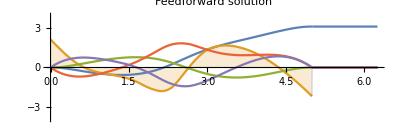
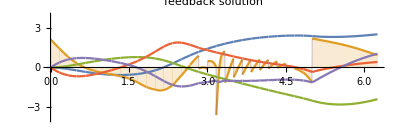
-Graphics- | -Graphics-

```mathematica
n=15;τ=5;τ1=τ*1.25;A=0.2;order = 4;maxIter = 100;maxError = 0.01;uMax = 5;maxCount = 5;maxJ = uMax^2*τ;InitGuess = {0,0,0,0};nFeedback = 30;
xdotMin = -2;xdotMax = 2;θMin = -π;θMax = π;θdotMin = -2;θdotMax = 2;
xdotInit = RandomReal[{xdotMin,xdotMax}];θInit = RandomReal[{θMin,θMax}];θdotInit = RandomReal[{θdotMin,θdotMax}];ICs = {0,xdotInit,θInit,θdotInit};
ICs = {0,0,0,0};
EInitial = Energy[Join[Table[ICs[[i]],{i,1,4}],{A}]];
Print["Initial Energy = ", EInitial];
systemData = {n,τ,τ1,A,order,maxIter,maxError,uMax,maxCount,InitGuess,maxJ} ;
{x1a,xdot1a,θ1a,θdot1a,u1a,λ1ff0,λ2ff0,λ3ff0,λ4ff0,Jff,K1}=ffCartPendulumLQR[ICs,systemData,nFeedback]; 
{x1c,xdot1c,θ1c,θdot1c,u1c,J}=testWithFBClipped[ICs,τ,τ1,x1a,xdot1a,θ1a,θdot1a,u1a,A,uMax,K1];
p1a=Plot[{θ1a[t],u1a[t],x1a[t],θdot1a[t],xdot1a[t]},{t,0,τ1},Filling->{2->Axis},PlotRange->{-4,4},PlotLegends->{"θ1a","u1a","x1a","θdot1a","xdot1a"},PlotLabel->"Feedforward solution ",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}];
p1c=Plot[{θ1c[t],u1c[t],x1c[t],θdot1c[t],xdot1c[t]},{t,0,τ1},PlotRange->{-4,4},Filling->{2->Axis},PlotLegends->{"θ1c","u1c","x1c","θdot1c","xdot1c"},PlotLabel->"feedback solution ",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}];
Grid[{{p1a,p1c}}]
```

Initial Energy = -0.2

Error First Guess = 1.81441×10^-15

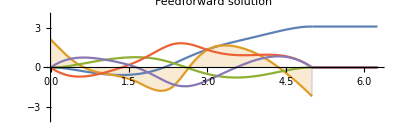
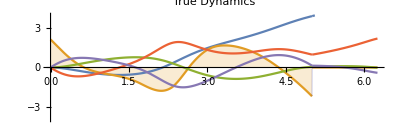
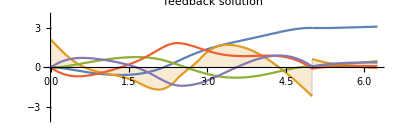
-Graphics- | -Graphics- | -Graphics-

```mathematica
n=15;τ=5;τ1=τ*1.25;A=0.2;order = 5;maxIter = 100;maxError = 0.01;uMax = 5;maxCount = 5;maxJ = uMax^2*τ;InitGuess = {0,0,0,0};
xdotMin = -2;xdotMax = 2;θMin = -π;θMax = π;θdotMin = -2;θdotMax = 2;
xdotInit = RandomReal[{xdotMin,xdotMax}];θInit = RandomReal[{θMin,θMax}];θdotInit = RandomReal[{θdotMin,θdotMax}];ICs = {0,xdotInit,θInit,θdotInit};
ICs = {0,0,0,0};
EInitial = Energy[Join[Table[ICs[[i]],{i,1,4}],{A}]];
Print["Initial Energy = ", EInitial];
systemData = {n,τ,τ1,A,order,maxIter,maxError,uMax,maxCount,InitGuess,maxJ} ;
{x1a,xdot1a,θ1a,θdot1a,u1a,λ1ff0,λ2ff0,λ3ff0,λ4ff0,Jff,K2}=ffCartPendulum[ICs,systemData]; 
{x1b,xdot1b,θ1b,θdot1b,u1b,J} = testSwingUp[ICs,τ,τ1,u1a,A];
{x1c,xdot1c,θ1c,θdot1c,u1c,J}=testWithFBClipped[ICs,τ,τ1,x1a,xdot1a,θ1a,θdot1a,u1a,A,uMax,K2];
p1a=Plot[{θ1a[t],u1a[t],x1a[t],θdot1a[t],xdot1a[t]},{t,0,τ1},Filling->{2->Axis},PlotRange->{-4,4},PlotLegends->{"θ1a","u1a","x1a","θdot1a","xdot1a"},PlotLabel->"Feedforward solution ",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}];
p1b=Plot[{θ1b[t],u1b[t],x1b[t],θdot1b[t],xdot1b[t]},{t,0,τ1},Filling->{2->Axis},PlotRange->{-4,4},PlotLegends->{"θ1b","u1b","x1b","θdot1b","xdot1b"},PlotLabel->"True Dynamics ",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}];
p1c=Plot[{θ1c[t],u1c[t],x1c[t],θdot1c[t],xdot1c[t]},{t,0,τ1},PlotRange->{-4,4},Filling->{2->Axis},PlotLegends->{"θ1c","u1c","x1c","θdot1c","xdot1c"},PlotLabel->"feedback solution ",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}];
Grid[{{p1a,p1b,p1c}}]
```

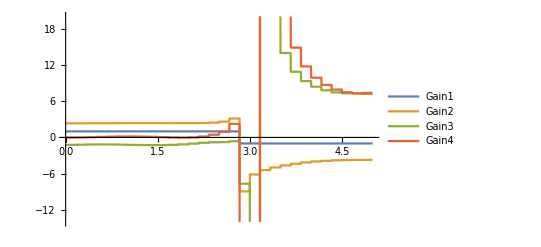

```mathematica
Plot[{K1[t][[1]],K1[t][[2]],K1[t][[3]],K1[t][[4]]},{t,0,τ},PlotLegends->{"Gain1","Gain2","Gain3","Gain4"}]
```

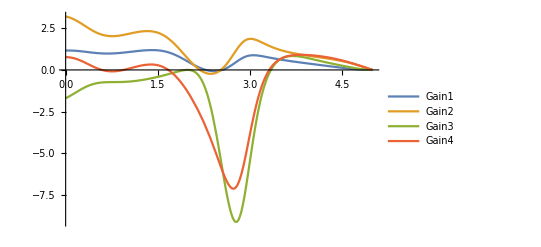

```mathematica
Plot[{K2[t][[1]],K2[t][[2]],K2[t][[3]],K2[t][[4]]},{t,0,τ},PlotLegends->{"Gain1","Gain2","Gain3","Gain4"},PlotRange->All]
```

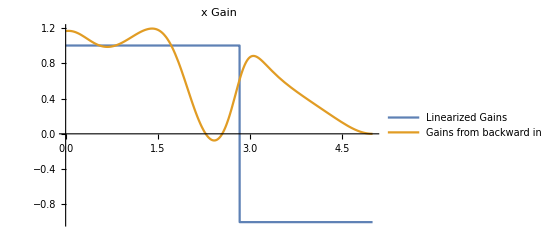
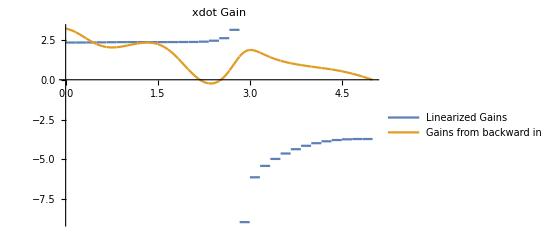
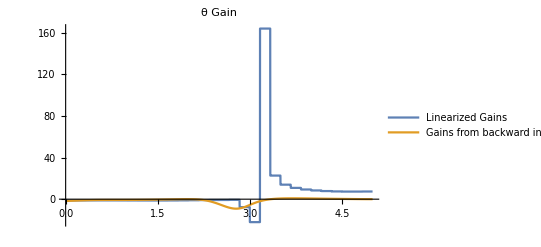
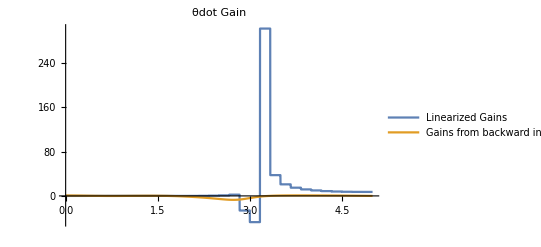
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
p1 = Plot[{K1[t][[1]],K2[t][[1]]},{t,0,τ},PlotLegends->{"Linearized Gains","Gains from backward integration"},PlotRange->All,PlotLabel->"x Gain",ImageSize->400];
p2 = Plot[{K1[t][[2]],K2[t][[2]]},{t,0,τ},PlotLegends->{"Linearized Gains","Gains from backward integration"},PlotRange->All,PlotLabel->"xdot Gain",ImageSize->400];
p3 = Plot[{K1[t][[3]],K2[t][[3]]},{t,0,τ},PlotLegends->{"Linearized Gains","Gains from backward integration"},PlotRange->All,PlotLabel->"θ Gain",ImageSize->400];
p4 = Plot[{K1[t][[4]],K2[t][[4]]},{t,0,τ},PlotLegends->{"Linearized Gains","Gains from backward integration"},PlotRange->All,PlotLabel->"θdot Gain",ImageSize->400];
Grid[{{p1,p2},{p3,p4}}]
```

### Understand the evolution of poles when using K = BackwardIntegrateRicatti

```mathematica
linearise[xff_,xdotff_,θff_,θdotff_,uff_,A_] := Module[{fx,nDim,xState ,x,xdot,θ,θdot,x2dot,θ2dot,u,L,Af,Bf,Cf,ssm,K,uStar,uFinal,i,j},
nDim = 4;
xState = {x,xdot,θ,θdot};
x2dot = 1/(1-A Cos[θ]^2) (u+A θdot^2 Sin[θ]+A Cos[θ] Sin[θ]);
θ2dot= 1/(1-A Cos[θ]^2) (-Sin[θ]-Cos[θ] (u+A θdot^2 Sin[θ]));
fx = {xdot,x2dot,θdot,θ2dot};
L = 1/2*u^2;
Af = Grad[fx,xState]; (* For nD stuff use Grad*)
Bf = D[fx,u] ;(*For 1D stuff use D*)
x = xff;xdot =   xdotff;θ =  θff;θdot =  θdotff;u = uff; 

{Af,Bf}
]
```

```mathematica
Poles[t_,x_,xdot_,θ_,θdot_,u_,A_,K2_] := Module[{Af,Bf,KGain},
{Af,Bf} = linearise[x[t],xdot[t],θ[t],θdot[t],u[t],A];
KGain = K2[t];
Eigenvalues[Af + KroneckerProduct[Bf,KGain]]]
Animate[ListPlot[ReIm/@Poles[t,x1a,xdot1a,θ1a,θdot1a,u1a,A,K2],PlotStyle->PointSize[Large],GridLines->Automatic,PlotRange->{{-5,5},{-5,5}}],{t,0,τ},AnimationRunning->False]
```

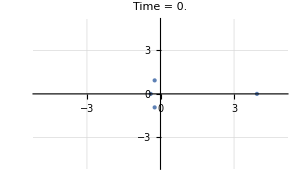
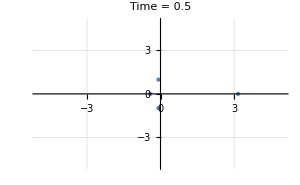
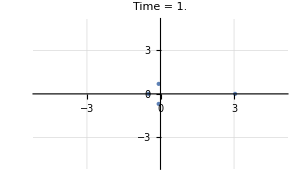
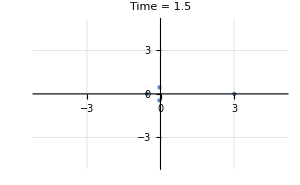
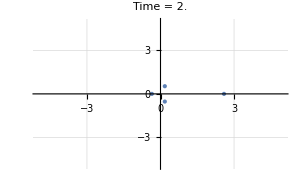
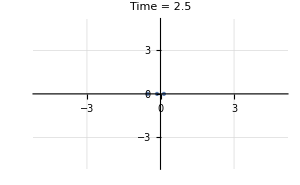
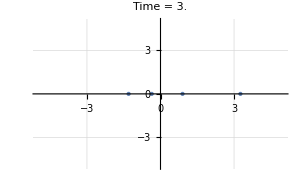
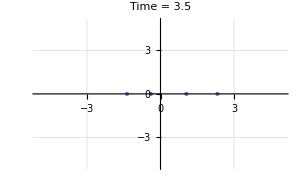
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |

```mathematica
polePlots = Table[ListPlot[ReIm/@Poles[t,x1a,xdot1a,θ1a,θdot1a,u1a,A,K2],PlotStyle->PointSize[Large],ImageSize->300,GridLines->Automatic,PlotRange->{{-5,5},{-5,5}},PlotLabel->StringJoin["Time = ",ToString[t]]],{t,0,5,0.5}];
numberPlots = Dimensions[polePlots][[1]];
Grid[Join[Table[Table[polePlots[[i]],{i,j,j+2}],{j,1,3*IntegerPart[numberPlots/3],3}],Table[Table[polePlots[[i]],{i,3*IntegerPart[numberPlots/3]+1,numberPlots}],{j,1,1}]]]
```